```mathematica
HartiganWongKMeans[data_List,k_Integer]:=Module[{n=Length[data],dims=Last@Dimensions[data],assignments,counts,centroids,sse,changed=True,iter=1,i,l,m,bestM,minDelta,deltaL,deltaM},(*1. Initial Assignment (Random)*)assignments=RandomInteger[{1,k},n];
(*2. Initial Centroids and Counts*)counts=Table[Count[assignments,j],{j,k}];
centroids=Table[If[counts[[j]]>0,Mean[Extract[data,Position[assignments,j]]],data[[RandomInteger[{1,n}]]]],{j,k}];
(*3. Main Loop*)While[changed&&iter<=10,changed=False;
iter++;
Do[l=assignments[[i]];
(*We cannot move a point if it's the only one in its cluster*)If[counts[[l]]>1,(*Calculate Delta for current cluster L*)deltaL=(counts[[l]]/(counts[[l]]-1.0))*Total[(data[[i]]-centroids[[l]])^2];
(*Find the best alternative cluster M*)minDelta=Infinity;
bestM=l;
Do[If[m!=l,deltaM=(counts[[m]]/(counts[[m]]+1.0))*Total[(data[[i]]-centroids[[m]])^2];
If[deltaM<minDelta,minDelta=deltaM;
bestM=m;];],{m,k}];
(*4. Transfer Step:If moving to M reduces SSE*)If[minDelta<deltaL,(*Update Centroids*)centroids[[l]]=(counts[[l]]*centroids[[l]]-data[[i]])/(counts[[l]]-1);
centroids[[bestM]]=(counts[[bestM]]*centroids[[bestM]]+data[[i]])/(counts[[bestM]]+1);
(*Update Counts and Assignment*)counts[[l]]--;
counts[[bestM]]++;
assignments[[i]]=bestM;
changed=True;];],{i,n}];];
<|"Assignments"->assignments,"Centroids"->centroids,"Iterations"->iter|>]
```

```mathematica
ModHart[data_List,k_Integer,maxIters_Integer:100]:=Module[{n=Length[data],dims=Last@Dimensions[data],assignments,counts,centroids,sse,changed=True,iter=1,i,l,m,bestM,minDelta,deltaL,deltaM},(*1. Initial Assignment (Random)*)assignments=RandomInteger[{1,k},n];
(*2. Initial Centroids and Counts*)counts=Table[Count[assignments,j],{j,k}];
centroids=Table[If[counts[[j]]>0,Mean[Extract[data,Position[assignments,j]]],data[[RandomInteger[{1,n}]]]],{j,k}];
(*3. Main Loop*)While[changed&&iter<=10,changed=False;
iter++;
Do[l=assignments[[i]];
(*We cannot move a point if it's the only one in its cluster*)If[counts[[l]]>1,(*Calculate Delta for current cluster L*)deltaL=(counts[[l]]/(counts[[l]]-1.0))*Total[(data[[i]]-centroids[[l]])^2];
(*Find the best alternative cluster M*)minDelta=Infinity;
bestM=l;
Do[If[m!=l,deltaM=(counts[[m]]/(counts[[m]]+1.0))*Total[(data[[i]]-centroids[[m]])^2];
If[deltaM<  minDelta,minDelta=deltaM;
bestM=m;];],{m,k}];
(*4. Transfer Step:If moving to M reduces SSE*)If[minDelta< (1.5-0.5(iter/maxIters))  deltaL,(*Update Centroids*)centroids[[l]]=(counts[[l]]*centroids[[l]]-data[[i]])/(counts[[l]]-1);
centroids[[bestM]]=(counts[[bestM]]*centroids[[bestM]]+data[[i]])/(counts[[bestM]]+1);
(*Update Counts and Assignment*)counts[[l]]--;
counts[[bestM]]++;
assignments[[i]]=bestM;
changed=True;];],{i,n}];];
<|"Assignments"->assignments,"Centroids"->centroids,"Iterations"->iter|>]
```

```mathematica
ModHart2[data_List,k_Integer,maxIters_Integer:100, init_]:=Module[{n=Length[data],dims=Last@Dimensions[data],assignments,counts,centroids,sse,changed=True,iter=1,i,l,m,bestM,minDelta,deltaL,deltaM},(*1. Initial Assignment (NonRandom)*)assignments=init;
(*2. Initial Centroids and Counts*)counts=Table[Count[assignments,j],{j,k}];
centroids=Table[If[counts[[j]]>0,Mean[Extract[data,Position[assignments,j]]],data[[RandomInteger[{1,n}]]]],{j,k}];
(*3. Main Loop*)While[changed&&iter<=10,changed=False;
iter++;
Do[l=assignments[[i]];
(*We cannot move a point if it's the only one in its cluster*)If[counts[[l]]>1,(*Calculate Delta for current cluster L*)deltaL=(counts[[l]]/(counts[[l]]-1.0))*Total[(data[[i]]-centroids[[l]])^2];
(*Find the best alternative cluster M*)minDelta=Infinity;
bestM=l;
Do[If[m!=l,deltaM=(counts[[m]]/(counts[[m]]+1.0))*Total[(data[[i]]-centroids[[m]])^2];
If[deltaM<  minDelta,minDelta=deltaM;
bestM=m;];],{m,k}];
(*4. Transfer Step:If moving to M reduces SSE*)If[minDelta< (1.5-0.5(iter/maxIters))  deltaL,(*Update Centroids*)centroids[[l]]=(counts[[l]]*centroids[[l]]-data[[i]])/(counts[[l]]-1);
centroids[[bestM]]=(counts[[bestM]]*centroids[[bestM]]+data[[i]])/(counts[[bestM]]+1);
(*Update Counts and Assignment*)counts[[l]]--;
counts[[bestM]]++;
assignments[[i]]=bestM;
changed=True;];],{i,n}];];
<|"Assignments"->assignments,"Centroids"->centroids,"Iterations"->iter|>]
```

```mathematica
testData=Join[RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],2000],RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],2000]];
```

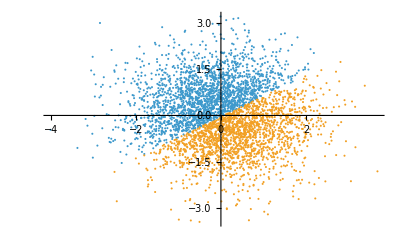
{5296.45,-Graphics-}

```mathematica
result=HartiganWongKMeans[testData,2];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

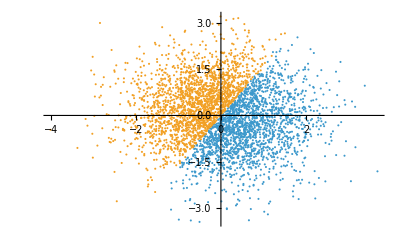
{5333.2,-Graphics-}

```mathematica
result=ModHart[testData,2,10];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

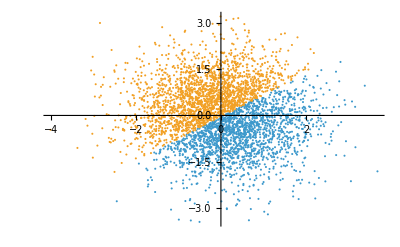
{5296.72,-Graphics-}

```mathematica
result=ModHart2[testData,2,10,result[[1]]];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

```mathematica
testData=RandomVariate[MultinormalDistribution[Table[0,{20}],IdentityMatrix[20]],2000];
```

```mathematica
result=HartiganWongKMeans[testData,20];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

{2997.94,-Graphics-}

```mathematica
result=ModHart[testData,20,10];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

{2823.89,-Graphics-}

```mathematica
result=ModHart2[testData,20,10,result[[1]]];cl1=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==1&]]];cl2=testData[[Select[Range[Length[result[[1]]]],result[[1,#]]==2&]]];m1=Mean[cl1];m2=Mean[cl2]; { Sum[Norm[cl1[[i]]-m1]^2, {i,1,Length[cl1]}]+  Sum[Norm[cl2[[i]]-m2]^2, {i,1,Length[cl2]}], ListPlot[{cl1,cl2}]}
```

{2743.92,-Graphics-}